```mathematica
RegionPlot[x y≥1/4,{x,-5,5},{y,-5,5},ImageSize->400]
```

-Graphics-

-Graphics-

{14.205,{0.39597,0.39594,0.39642,0.39774,0.39626,0.39786,0.39743,0.39802,0.39807,0.3945,0.39619,0.39382,0.39796,0.3971,0.39709,0.39667,0.39879,0.39669,0.39791,0.39694,0.39707,0.39181,0.39642,0.39688,0.39737,0.39329,0.3959,0.39614,0.39696,0.39549,0.39755,0.39788,0.39637,0.39829,0.39675,0.39613,0.39782,0.3989,0.39202,0.39597,0.39771,0.39604,0.39587,0.39674,0.39695,0.39682,0.39724,0.39388,0.398,0.39668,0.39488,0.39865,0.39754,0.39476,0.39657,0.39757,0.39568,0.39696,0.39763,0.39632,0.39486,0.39649,0.39814,0.3938,0.39231,0.3959,0.39784,0.39809,0.39475,0.39701,0.39921,0.40056,0.39571,0.3974,0.39665,0.39577,0.3939,0.39734,0.3991,0.39437,0.39657,0.39285,0.39603,0.39484,0.39573,0.39556,0.39599,0.39596,0.39784,0.39758,0.39871,0.39847,0.40078,0.39675,0.39417,0.39704,0.39715,0.39705,0.39855,0.39987}}

0.396616

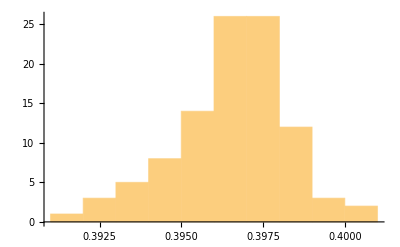

```mathematica
RegionPlot[(Tan[x]^2) (Cot[y]^2)>3,{x,-5,5},{y,-5,5},ImageSize->400]
(dataset1=Table[nMax1=100000;
1.0 (Table[If[((Tan[RandomReal[{-5,5}]])^2) ((Cot[RandomReal[{-5,5}]])^2)>3,1,0],nMax1]//Total)/nMax1,{100}])//Timing
Mean[dataset1]
Histogram[dataset1]
```

-Graphics-

{42.679,{0.24618,0.24928,0.24709,0.24594,0.2473,0.2492,0.24707,0.24914,0.24898,0.2484,0.24798,0.24655,0.24737,0.24687,0.25025,0.24886,0.24836,0.2449,0.24846,0.24881,0.24859,0.2489,0.24942,0.2494,0.24769,0.24675,0.24894,0.24685,0.24979,0.24844,0.2485,0.24797,0.24784,0.24874,0.24877,0.24972,0.24691,0.24817,0.24837,0.24857,0.24774,0.24723,0.24749,0.24702,0.24947,0.24803,0.24838,0.24998,0.24917,0.2463,0.24809,0.24965,0.24815,0.24813,0.2497,0.24899,0.24735,0.24847,0.24929,0.24872,0.24796,0.24842,0.24778,0.24848,0.2482,0.24822,0.24649,0.24739,0.2472,0.2476,0.24643,0.24784,0.2493,0.24911,0.24913,0.25018,0.2504,0.24896,0.25118,0.24846,0.24566,0.24602,0.24803,0.24789,0.24843,0.24727,0.24788,0.2492,0.24968,0.24642,0.24978,0.24665,0.24607,0.24751,0.24838,0.24592,0.25059,0.24833,0.24682,0.24587}}

0.248138

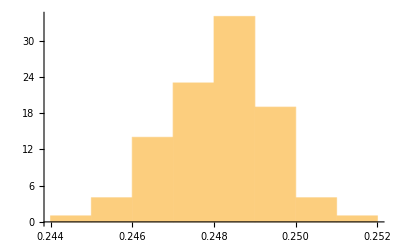

12.1588

```mathematica
RegionPlot[{x^2-y^3<1,y^2-x^3<1},{x,-2,5},{y,-2,5}]
(dataset2=Table[nMax2=100000;
1.0 (Table[s=RandomReal[{-2,5}];t=RandomReal[{-2,5}];
If[s^2-t^3<1&&t^2-s^3<1,1,0],nMax2]//Total)/nMax2,{100}])//Timing
Mean[dataset2]
Histogram[dataset2]
49*Mean[dataset2]
```

```mathematica
RegionPlot[{(x^2)+(y^2)=1,2 x^2+(y^2)/2=1},{x,-5,5},{y,-5,5}];
(dataset3=Table[nMax3=10000;
1.0 (Table[v=RandomReal[{-2,5}];w=RandomReal[{-2,5}];
{If[(v^2+w^2) (2 v^2+(w^2)/2)=1,1,0]},nMax3]//Total)/nMax3,{100}])//Timing
Mean[dataset3]
Histogram[dataset3]
```

Set::write: Tag Plus in x^2+y^2 is Protected.

Set::write: Tag Plus in 2 x^2+y^2/2 is Protected.

Set::write: Tag Plus in x^2+y^2 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

ImplicitRegion::bcond: 1 should be a Boolean combination of equations, inequalities, and Element statements.

Set::write: Tag Times in 15.7499 26.9291 is Protected.

Set::write: Tag Times in 12.5732 16.7145 is Protected.

Set::write: Tag Times in 4.48076 4.90565 is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

{9.965,{{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]},{1. If[1,1,0]}}}

{1. If[1,1,0]}

-Graphics-